# QKT quantum

## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\INVESTIGACION\2024\Notebooks QKT

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
(*Operadores*)
Clear[Sz,SM,Sm,Sx,a2,Sy,F];

Sz[J_]:=DiagonalMatrix[Table[-J+k-1,{k,1,2J+1}]];
SM[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i+1)],{i,-J,J-1}],1];
Sm[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i-1)],{i,-J+1,J}],-1];
Sx[J_]:=(1/2)(SM[J]+Sm[J]);
Sy[J_]:=Sy[J]=(1/(2I))(SM[J]-Sm[J]);
(*Estados coherentes*)


Clear[Tq];
Tq[q_]:=Module[{a,b,points=allpointsx[[q]]},
{a,b}=CoefficientList[Fit[points,{1,x},x],x];
{qlist[[q]],-b}
];

Clear[IPR];
IPR[J_,q_,ini_]:=Module[{a},
Log[Total[Abs[Conjugate[eigen].ini]^(2q)]]
];

Clear[Dq];
Dq[Q_,P_,q_,J_]:=Module[{floq=eigen,cohe=Quiet[a2[J,Q,P]],a},
a=(1/(1-q))Log[Total[Abs[Conjugate[floq].cohe]^(2q)]]/Log[2J+1]
];

Clear[H];
H[J_,α_,k_]:=N[(k/(2J))(Sx[J].Sx[J])+(α)(Sz[J])];

Clear[Qp,Q,P];
Qp[J_]:=DiagonalMatrix[Table[Sqrt[i/2],{i,IntegerPart[2J]}],-1];
Q[J_]:=Qp[J]+Transpose[Qp[J]];
P[J_]:=-I(Qp[J]-Transpose[Qp[J]]);
```

```mathematica
Clear[F,Fun];

F[α_,k_,s_]:=Module[{a,sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}
];

Fun[α_,k_,s_]:=Module[{sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}.s
];

Clear[change];
change[s_]:=Module[{B=Sqrt[2/(1-s[[3]])]},
{s[[1]]*B,s[[2]]*B}
];

Clear[change2];
change2[Q_]:=Module[{B=Norm[Q]},
{Q[[1]]*Sqrt[1-(1/4)B^2],Q[[2]]*Sqrt[1-(1/4)B^2],(1/2)B^2 -1}
];

Clear[mapeo];
mapeo[Qini_,α_,k_,n_]:=Module[{a,list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Fun[α,k,#]&,s,n];
Map[change[#]&,list]
];

mapeob[Qini_,α_,k_,n_]:=Module[{map={},snew,a,s,Qnew},
AppendTo[map,Qini];
s=change2[Qini];
Do[
snew=MatrixPower[N[F[α,k,s]],2].s;
AppendTo[map,change[snew]];
s=snew;
,{l,1,n}];
map
];

Clear[Jx,Jy,Jz,M,mapeo1,jmas];
Jx[x_,y_,z_,α_,k_]:=x*Cos[α]-y*Sin[α]*Cos[k*x]+z*Sin[α]*Sin[k*x];
Jy[x_,y_,z_,α_,k_]:=x*Sin[α]+y*Cos[α]*Cos[k*x]-z*Cos[α]*Sin[k*x];
Jz[x_,y_,z_,α_,k_]:=y*Sin[k*x]+z*Cos[k*x];

M[Jini_,α_Real,k_Real]:=Module[{M},
M={{D[Jx[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},
{D[Jy[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},{D[Jz[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}}}//N;
M
];

mapeo1[si_,α_,k_,n_]:=Module[{s=si},
MatrixPower[F[α,k,s],n].s
];
```

## 1 qubit

```mathematica
Clear[a2];
a2[J_,Q_,P_]:=Module[{z=-1+(Q^2+P^2)/2,ϕ=ArcTan[-(P/Q)]},
Table[1/((1+Tan[ArcCos[-z]/2]^2)^J)Sqrt[Binomial[2J,J+(m-J)]] Tan[ArcCos[-z]/2]^(J+(m-J))Exp[-I(J+(m-J))ϕ],{m,0,2J}]
];

Clear[F];
F[J_,α_,k_,τ_]:=MatrixExp[(-I*k/(2J))(Sx[J].Sx[J])].MatrixExp[(-I*α*τ)(Sz[J])];
```

```mathematica
J=1/2;
τ=1;
```

```mathematica
Clear[Q,P];
Q=1;
P=0;
```

```mathematica
cohe=a2[J,Q,P];
```

```mathematica
cohe
```

{(√3)/2,1/2}

```mathematica
Clear[α,k];
mat=F[J,α,k,τ];
```

```mathematica
mat//MatrixForm
```

(ⅇ^(-(ⅈ k)/4+(ⅈ α)/2) | 0
0 | ⅇ^(-(ⅈ k)/4-(ⅈ α)/2))

```mathematica
{eigenval,eigenvec}=Eigensystem[F[J,α,k,τ]];
```

```mathematica
eigenval//FullSimplify
```

{ⅇ^(-1/4 ⅈ (k+2 α)),ⅇ^(-1/4 ⅈ (k-2 α))}

```mathematica
eigenvec//FullSimplify
```

{{0,1},{1,0}}

# Reduced qubit

## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\INVESTIGACION\2024\Magic

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
(*Operadores*)
Clear[Sz,SM,Sm,Sx,Sy];

Sz[J_]:=DiagonalMatrix[Table[-J+k-1,{k,1,2J+1}]];
SM[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i+1)],{i,-J,J-1}],1];
Sm[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i-1)],{i,-J+1,J}],-1];
Sx[J_]:=(1/2)(SM[J]+Sm[J]);
Sy[J_]:=Sy[J]=(1/(2I))(SM[J]-Sm[J]);
(*Estados coherentes*)


Clear[Tq];
Tq[q_]:=Module[{a,b,points=allpointsx[[q]]},
{a,b}=CoefficientList[Fit[points,{1,x},x],x];
{qlist[[q]],-b}
];

Clear[IPR];
IPR[J_,q_,ini_]:=Module[{a},
Log[Total[Abs[Conjugate[eigen].ini]^(2q)]]
];

Clear[Dq];
Dq[Q_,P_,q_,J_]:=Module[{floq=eigen,cohe=Quiet[a2[J,Q,P]],a},
a=(1/(1-q))Log[Total[Abs[Conjugate[floq].cohe]^(2q)]]/Log[2J+1]
];

Clear[H];
H[J_,α_,k_]:=N[(k/(2J))(Sx[J].Sx[J])+(α)(Sz[J])];

Clear[Qp,Q,P];
Qp[J_]:=DiagonalMatrix[Table[Sqrt[i/2],{i,IntegerPart[2J]}],-1];
Q[J_]:=Qp[J]+Transpose[Qp[J]];
P[J_]:=-I(Qp[J]-Transpose[Qp[J]]);
Clear[a2];
a2[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J,J}],20]]
];

Clear[Floq];
Floq[J_,α_,k_,τ_]:=MatrixExp[(-I*k/(2J))(Sx[J].Sx[J])].MatrixExp[(-I*α*τ)(Sz[J])];
```

## Single spin J

## Reduced density matrix

```mathematica
Clear[CG];
CG[n1_,n_,N1_,N2_]:=CG[n1,n,N1,N2]=Binomial[N1,n1]*Binomial[N2,n-n1]/Binomial[N1+N2,n];
Clear[bloch];
bloch[rho_]:={2Re[rho[[1,2]]],-2Im[rho[[1,2]]],rho[[1,1]]-rho[[2,2]]};
(*Plot Bloch sphere with Bloch vector*)
plotsphere=SphericalPlot3D[1,{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.1],PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False];
```

```mathematica
Clear[Floq];
Floq[J_,α_,k_,τ_]:=MatrixExp[(-I*k/(2J))(Sx[J].Sx[J])].MatrixExp[(-I*α*τ)(Sz[J])];
(*Floq[J_,α_,k_,τ_]:=MatrixExp[(-I*k/(2J))(Sx[J].Sx[J])].MatrixExp[(-I*α*τ)(Sz[J])];*)
(*Floq[J_,α_,k_,τ_]:=MatrixExp[(-I*k/(2J))(Sx[J].Sx[J])].MatrixExp[(-I*α*τ)(Sz[J]+0.001*Sx[J])];*)
```

```mathematica
α=0.84;
k=30;
τ=1;
```

```mathematica
Clear[J,N1,N2];
J=100.0;
N1=1;
N2=2J-N1;
rhos={};
rho=ConstantArray[0,{N1+1,N1+1}];
```

```mathematica
Clear[mat,neweigenvec];
mat=Floq[J,α,k,τ];
matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
matm=Table[mat[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
{eigenvalM,eigenvecM}=Eigensystem[matM];
{eigenvalm,eigenvecm}=Eigensystem[matm];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
(*mat=Floq[N[J],α,k,τ];
neweigenvec=Orthogonalize[Eigenvectors[mat]];*)
```

```mathematica
(*Clear[basis,newbasis];
ope=Sx[J];
basis=Eigenvectors[N[ope]];
newbasis=ParallelTable[Conjugate[basis].i,{i,neweigenvec}];
neweigenvec=newbasis;*)
```

```mathematica
rhos={};
Do[
b=neweigenvec[[i]];
Do[
rho[[i,j]]=Sum[ b[[i+n2-1]]*Conjugate[b[[j+n2-1]]]*Sqrt[CG[i-1,i+n2-2,N1,N2]*CG[j-1,j+n2-2,N1,N2]],{n2,1,N2+1}];
rho[[j,i]]=Conjugate[rho[[i,j]]];
,{i,1,N1+1},{j,i,N1+1}];
AppendTo[rhos,Chop[rho]];
,{i,Length[neweigenvec]}];
```

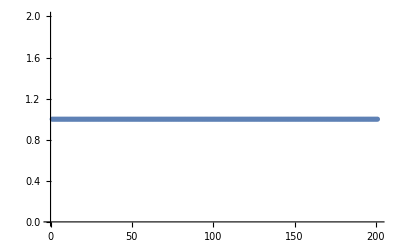

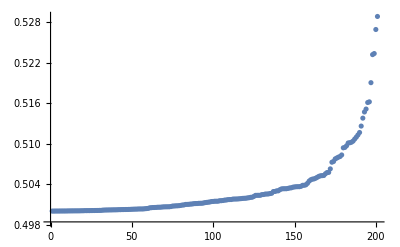

```mathematica
Table[Tr[i],{i,rhos}]//ListPlot
ListPlot[Sort[Table[Chop[Tr[i.i]],{i,rhos}]],PlotRange->All]
```

```mathematica
blochs=Table[bloch[i],{i,rhos}];
plotpuntos=ListPointPlot3D[blochs,ColorFunction->"Rainbow",PlotRange->All,AspectRatio->1,PlotTheme->"Detailed",BoxRatios->{1, 1, 1},AxesLabel->{Style["x",Black,25],Style["y",Black,25],Style["z",Black,25]}];
Show[plotpuntos,plotsphere,ImageSize->400,PlotLabel->Style["k = "<>ToString[N[k]]<>", N = "<>ToString[J]<>", n1 = "<>ToString[N1],25,Black]]
```

-Graphics3D-

```mathematica
blochs=Table[bloch[i],{i,rhos}];
plotpuntos=ListPointPlot3D[blochs,ColorFunction->"Rainbow",PlotRange->All,AspectRatio->1,PlotTheme->"Detailed",BoxRatios->{1, 1, 1},AxesLabel->{Style["x",Black,25],Style["y",Black,25],Style["z",Black,25]}];
Show[plotpuntos,plotsphere,ImageSize->400,PlotLabel->Style["k = "<>ToString[N[k]]<>", N = "<>ToString[J]<>", n1 = "<>ToString[N1],25,Black]]
```

-Graphics3D-

```mathematica
blochs=Table[bloch[i],{i,rhos}];
plotpuntos=ListPointPlot3D[blochs,ColorFunction->"Rainbow",PlotRange->All,AspectRatio->1,PlotTheme->"Detailed",BoxRatios->{1, 1, 1},AxesLabel->{Style["x",Black,25],Style["y",Black,25],Style["z",Black,25]}];
Show[plotpuntos,plotsphere,ImageSize->400,PlotLabel->Style["k = "<>ToString[N[k]]<>", N = "<>ToString[J]<>", n1 = "<>ToString[N1],25,Black]]
```

-Graphics3D-

## Reduced density matrix coherent states

```mathematica
Clear[CG];
CG[n1_,n_,N1_,N2_]:=CG[n1,n,N1,N2]=Binomial[N1,n1]*Binomial[N2,n-n1]/Binomial[N1+N2,n];
Clear[bloch];
bloch[rho_]:={2Re[rho[[1,2]]],-2Im[rho[[1,2]]],rho[[1,1]]-rho[[2,2]]};
(*Plot Bloch sphere with Bloch vector*)
plotsphere=SphericalPlot3D[1,{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.1],PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False];
```

```mathematica
Clear[J,N1,N2];
J=20;
N1=1;
N2=2J-N1;
rhos={};
rho=ConstantArray[0,{N1+1,N1+1}];
```

```mathematica
cohes=Table[a2[J,i,0],{i,-2+1/10,2-1/10,1/10}];
```

```mathematica
rhos={};
Do[
b=cohes[[k]];
Do[
rho[[i,j]]=Sum[ b[[i+n2-1]]*Conjugate[b[[j+n2-1]]]*Sqrt[CG[i-1,i+n2-2,N1,N2]*CG[j-1,j+n2-2,N1,N2]],{n2,1,N2+1}];
rho[[j,i]]=Conjugate[rho[[i,j]]];
,{i,1,N1+1},{j,i,N1+1}];
AppendTo[rhos,Chop[rho]];
,{k,Length[cohes]}];
```

```mathematica
trazas=Table[N[Tr[i]],{i,rhos}]
linearentr=Table[Chop[N[Tr[i.i]]],{i,rhos}]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

{0.501534,0.500084,0.500014,0.503821,0.50008,0.50143,0.523195,0.515126,0.500347,0.502338,0.500224,0.502442,0.505276,0.501541,0.502999,0.509686,0.505712,0.500627,0.500106,0.501797,0.500034,0.501637,0.50343,0.500234,0.500244,0.507998,0.500172,0.500572,0.502909,0.500069,0.500839,0.500078,0.501897,0.502171,0.509381,0.500674,0.500212,0.505152,0.503313,0.510967,0.500311,0.500616,0.508321,0.504875,0.502329,0.501712,0.500194,0.500637,0.500006,0.500186,0.501159,0.500026,0.500226,0.501708,0.500316,0.502345,0.500256,0.501821,0.500064,0.50003,0.5,0.500319,0.500236,0.500006,0.501351,0.50018,0.500897,0.500547,0.528853,0.511287,0.501196,0.503617,0.500315,0.506258,0.500208,0.501842,0.500585,0.514693,0.501038,0.501255,0.501465,0.504639,0.501772,0.501146,0.503363,0.500993,0.500746,0.500372,0.505257,0.503581,0.501159,0.516098,0.500501,0.513778,0.501414,0.500984,0.500172,0.500163,0.502544,0.503893,0.500036,0.500633,0.500137,0.510679,0.505734,0.503671,0.503171,0.509441,0.503002,0.500092,0.500034,0.500001,0.503286,0.50501,0.507734,0.50009,0.510375,0.502056,0.501946,0.500638,0.51013,0.500038,0.500006,0.501789,0.52692,0.511651,0.519036,0.500048,0.503314,0.504771,0.503541,0.501094,0.503608,0.500187,0.500025,0.501693,0.502646,0.500065,0.512602,0.500293,0.501628,0.505531,0.501877,0.501049,0.503446,0.502456,0.507245,0.501285,0.501319,0.50078,0.502899,0.501115,0.504739,0.501463,0.500532,0.505232,0.500802,0.500906,0.50198,0.502038,0.500012,0.50331,0.500069,0.500281,0.502603,0.510099,0.500271,0.507867,0.502525,0.516196,0.500751,0.500572,0.500526,0.501905,0.504121,0.502339,0.501567,0.523356,0.500778,0.500161,0.500048,0.50029,0.501119,0.500017,0.500012,0.507355,0.503616,0.510209,0.500151,0.50003,0.504444,0.500102,0.501461,0.508087,0.503828,0.500015,0.500399,0.500483,0.501787,0.50253,0.501004}

```mathematica
blochs=Table[bloch[i],{i,rhos}];
plotpuntos=ListPointPlot3D[blochs,ColorFunction->"Rainbow",PlotRange->All,AspectRatio->1];
Show[plotsphere,plotpuntos,ImageSize->400,PlotLabel->Style["k = "<>ToString[N[k]]<>", N = "<>ToString[J]<>", n1 = "<>ToString[N1],25,Black]]
```

-Graphics3D-

## Reduced density matrix evolved coherent states

```mathematica
Clear[CG];
CG[n1_,n_,N1_,N2_]:=CG[n1,n,N1,N2]=Binomial[N1,n1]*Binomial[N2,n-n1]/Binomial[N1+N2,n];
Clear[bloch];
bloch[rho_]:={2Re[rho[[1,2]]],-2Im[rho[[1,2]]],rho[[1,1]]-rho[[2,2]]};
(*Plot Bloch sphere with Bloch vector*)
plotsphere=SphericalPlot3D[1,{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.1],PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False];
```

```mathematica
Clear[J,N1,N2];
J=20;
N1=1;
N2=2J-N1;
rhos={};
rho=ConstantArray[0,{N1+1,N1+1}];
```

```mathematica
k=13/10;
α=0.84;
τ=1.0;
```

```mathematica
cohe=a2[J,1,1];
cohet=Table[MatrixPower[Floq[N[J],α,k,τ],n].cohe,{n,50}];
```

```mathematica
Do[
b=k;
Do[
rho[[i,j]]=Sum[ b[[i+n2-1]]*Conjugate[b[[j+n2-1]]]*Sqrt[CG[i-1,i+n2-2,N1,N2]*CG[j-1,j+n2-2,N1,N2]],{n2,1,N2+1}];
rho[[j,i]]=Conjugate[rho[[i,j]]];
,{i,1,N1+1},{j,i,N1+1}];
AppendTo[rhos,rho];
,{k,cohet}];
```

```mathematica
trazas=Table[N[Tr[i]],{i,rhos}]//Chop
linearentr=Table[Chop[N[Tr[i.i]]],{i,rhos}]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

{1.,0.993375,0.945089,0.861289,0.851312,0.845781,0.786871,0.708861,0.69959,0.698546,1.,0.993375,0.945089,0.861289,0.851312,0.845781,0.786871,0.708861,0.69959,0.698546,1.,0.993375,0.945089,0.861289,0.851312,0.845781,0.786871,0.708861,0.69959,0.698546,0.653552,0.609177,0.604615,0.606191,0.589325,0.573006,0.571747,0.572238,0.566848,0.562935,0.564329,0.564745,0.562935,0.562272,0.561088,0.556824,0.556244,0.559336,0.561932,0.561358,0.564035,0.563689,0.559217,0.55957,0.55926,0.555862,0.560318,0.564913,0.560665,0.563178,0.563517,0.552937,0.560931,0.557471,0.556889,0.568715,0.557203,0.569824,0.558824,0.561998}

```mathematica
blochs=Table[bloch[i],{i,Chop[rhos]}];
plotpuntos=ListPointPlot3D[blochs,ColorFunction->"Rainbow",PlotRange->All,AspectRatio->1];
Show[plotsphere,plotpuntos,ImageSize->400,PlotLabel->Style["k = "<>ToString[N[k]]<>", N = "<>ToString[J]<>", n1 = "<>ToString[N1],25,Black]]
```

-Graphics3D-